```mathematica
jac={{s1,0,s2,0},{0,s1,0,s2},{s2,0,-1+s1,0},{0,s2,0,-1+s1}};
jac//MatrixForm
jac//Eigenvalues//Simplify
```

(s1 | 0 | s2 | 0
0 | s1 | 0 | s2
s2 | 0 | -1+s1 | 0
0 | s2 | 0 | -1+s1)

{-1/2+s1-1/2 √(1+4 s2^2),-1/2+s1-1/2 √(1+4 s2^2),1/2 (-1+2 s1+√(1+4 s2^2)),1/2 (-1+2 s1+√(1+4 s2^2))}

```mathematica
Solve[-1/2+s1-1/2 √(1+4 s2^2)==0,s1]//Simplify
```

{{s1→1/2 (1+√(1+4 s2^2))}}

```mathematica
Solve[-1/2+s1+1/2 √(1+4 s2^2)==0,s1]//Simplify
```

{{s1→1/2 (1-√(1+4 s2^2))}}

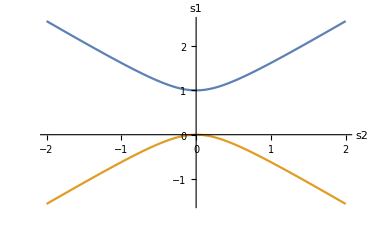

```mathematica
Plot[{1/2 (1+√(1+4 s2^2)),1/2 (1-√(1+4 s2^2))},{s2, -2,2},AxesLabel->{s2, s1}]
```

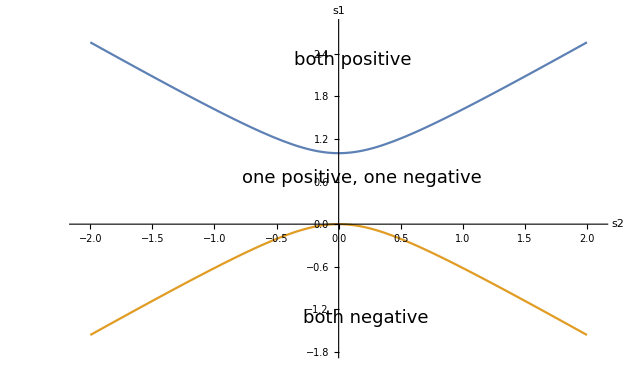

```mathematica
Det[jac]//Simplify
```

(s1-s1^2+s2^2)^2

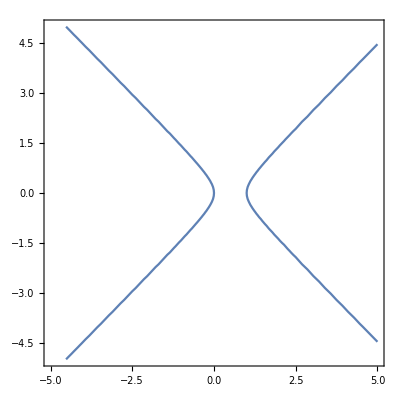

```mathematica
ContourPlot[s1-s1^2+s2^2==0,{s1, -5,5},{s2,-5,5}]
```

```mathematica
LinearSolve[jac, {0,0,0,0}]
```

{0,0,0,0}